```mathematica
Table[Labeled[allGraphs4[z,"graph"],Style[z,ColourForKey[allGraphs4,z]] ],{z,Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]==Table[{k},{k,1,4}]&&EdgeCount[allGraphs4[#,"graph"]]==4&]}]
```

{-Graphics-360,-Graphics-354,-Graphics-352,-Graphics-336,-Graphics-334,-Graphics-328,-Graphics-282,-Graphics-280,-Graphics-274,-Graphics-256,-Graphics-120,-Graphics-118,-Graphics-112,-Graphics-94,-Graphics-40}

```mathematica
Beat[k_]:=Labeled[allGraphs4[k,"graph"],Style[k,ColourForKey[allGraphs4,k]] ]
```

```mathematica
Table[Labeled[allGraphs4[z,"graph"],Style[z,ColourForKey[allGraphs4,z]] ],{z,Select[Keys[allGraphs4],allGraphs4[#,"vertexsets"]==Table[{k},{k,1,4}]&&EdgeCount[allGraphs4[#,"graph"]]==5&]}]
```

{-Graphics-363,-Graphics-361,-Graphics-355,-Graphics-337,-Graphics-283,-Graphics-121}

```mathematica
rep4=Table[allGraphs4[k,"colofour"]->Beat[k],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→-Graphics-364,v1x2x34→-Graphics-365,v1x24x3→-Graphics-367,v1x23x4→-Graphics-373,v1x234→-Graphics-377,v14x2x3→-Graphics-391,v14x23→-Graphics-400,v13x2x4→-Graphics-445,v13x24→-Graphics-448,v134x2→-Graphics-473,v12x3x4→-Graphics-607,v12x34→-Graphics-608,v124x3→-Graphics-637,v123x4→-Graphics-697,v1234→-Graphics-728}

```mathematica
rep4Val=Table[allGraphs4[k,"colofour"]->Style[ChromaticPolynomial[allGraphs4[k,"graph"],4],Red],{k,allGraphs4AtomKeys}]
```

{v1x2x3x4→24,v1x2x34→24,v1x24x3→24,v1x23x4→24,v1x234→12,v14x2x3→24,v14x23→12,v13x2x4→24,v13x24→12,v134x2→12,v12x3x4→24,v12x34→12,v124x3→12,v123x4→12,v1234→4}

```mathematica
(((x-2)*allGraphs4[280,"colofour"]-(allGraphs4[361,"colofour"]+allGraphs4[283,"colofour"])/.x ->4//FullSimplify)/.rep4)//TraditionalForm
```

-Graphics-367+-Graphics-445+2 -Graphics-448

```mathematica
(((x-2)*allGraphs4[280,"colofour"]-(allGraphs4[361,"colofour"]+allGraphs4[283,"colofour"])/.rep4Val//FullSimplify))
```

(-2+x) 12+(-10+3 x) 24

## Now with 5 nodes

```mathematica
Table[Labeled[allGraphs5[z,"graph"],Style[z,ColourForKey[allGraphs5,z]] ],{z,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[g,CycleGraph[5]]
&&EdgeQ[g,1<->2]
&&EdgeQ[g,2<->3]
&&EdgeQ[g,3<->4]
&&EdgeQ[g,4<->5]
&&EdgeQ[g,5<->1]
]
&]}]
```

{-Graphics-20665}

```mathematica
Table[Labeled[allGraphs5[z,"graph"],Style[z,ColourForKey[allGraphs5,z]] ],{z,Select[Keys[allGraphs5],
With[{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[g,EdgeAdd[CycleGraph[5],{1<->3,1<->4}]]
&&EdgeQ[g,1<->2]
&&EdgeQ[g,2<->3]
&&EdgeQ[g,3<->4]
&&EdgeQ[g,4<->5]
&&EdgeQ[g,5<->1]
]&]}]
```

{-Graphics-29413,-Graphics-27229,-Graphics-22933,-Graphics-20773,-Graphics-20695}

```mathematica
Table[Labeled[allGraphs5[z,"graph"],Style[z,ColourForKey[allGraphs5,z]] ],{z,Select[Keys[allGraphs5],
With[{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[g,EdgeAdd[CycleGraph[5],{1<->3}]]
&&EdgeQ[g,1<->2]
&&EdgeQ[g,2<->3]
&&EdgeQ[g,3<->4]
&&EdgeQ[g,4<->5]
&&EdgeQ[g,5<->1]
]&]}]
```

```mathematica
Beat5[k_]:=Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]] ]
```

```mathematica
rep5=Table[allGraphs5[k,"colofour"]->Beat5[k],{k,allGraphs5AtomKeys}];
```

```mathematica
rep5Null=Table[allGraphs5[k,"colofourrealnull"]->Beat5[k],{k,allGraphs5NullAtomKeys}];
```

```mathematica
((((x-3)*allGraphs5[20665,"colofour"]-(allGraphs5[29413,"colofour"]+allGraphs5[20773,"colofour"]+allGraphs5[20668,"colofour"])/.x ->4)//FullSimplify)/.rep5)
```

--Graphics-36085--Graphics-31711--Graphics-29605--Graphics-29551--Graphics-29527-2 -Graphics-29524

```mathematica
((((x-3)*allGraphs5[20665,"graph"]-(allGraphs5[29413,"graph"]+allGraphs5[20773,"graph"]+allGraphs5[20668,"graph"]))))
```

```mathematica
allGraphs5[20665,"colofour"]/.rep5
```

```mathematica
allGraphs5[29413,"colofour"]/.rep5
```

-Graphics-29608+-Graphics-29605+-Graphics-29551+-Graphics-29527+-Graphics-29524

```mathematica
(allGraphs5[29413,"colofour"]+allGraphs5[20773,"colofour"]+allGraphs5[20668,"colofour"])/.rep5
```

-Graphics-36166+-Graphics-36112+-Graphics-31738+-Graphics-31714+-Graphics-29608+2 -Graphics-36085+2 -Graphics-31711+2 -Graphics-29605+2 -Graphics-29551+2 -Graphics-29527+3 -Graphics-29524

```mathematica
((x-2)*allGraphs5[20665,"colofour"])/.rep5
```

(-2+x) (-Graphics-36166+-Graphics-36112+-Graphics-31738+-Graphics-31714+-Graphics-29608+-Graphics-36085+-Graphics-31711+-Graphics-29605+-Graphics-29551+-Graphics-29527+-Graphics-29524)

```mathematica
FullSimplify[((x-2)*allGraphs5[20665,"colofour"]-(allGraphs5[29413,"colofour"]+allGraphs5[20773,"colofour"]+allGraphs5[20668,"colofour"]))/.x ->3]/.rep5
```

--Graphics-36085--Graphics-31711--Graphics-29605--Graphics-29551--Graphics-29527-2 -Graphics-29524

```mathematica
((x-2)*allGraphs5[20665,"colofour"]-(allGraphs5[29413,"colofour"]+allGraphs5[20773,"colofour"]+allGraphs5[20668,"colofour"]))/.x ->4/.rep5
```

--Graphics-36166--Graphics-36112--Graphics-31738--Graphics-31714--Graphics-29608-2 -Graphics-36085-2 -Graphics-31711-2 -Graphics-29605-2 -Graphics-29551-2 -Graphics-29527-3 -Graphics-29524+2 (-Graphics-36166+-Graphics-36112+-Graphics-31738+-Graphics-31714+-Graphics-29608+-Graphics-36085+-Graphics-31711+-Graphics-29605+-Graphics-29551+-Graphics-29527+-Graphics-29524)

```mathematica
FullSimplify[(((x-2)*allGraphs5[20665,"colofourrealnull"]-(allGraphs5[29413,"colofourrealnull"]+allGraphs5[20773,"colofourrealnull"]+allGraphs5[20668,"colofourrealnull"]))/.x ->4)==0]/.rep5Null
```

14 -Graphics-59048+2 -Graphics-52974+2 -Graphics-43902+-Graphics-39384+2 -Graphics-40878+-Graphics-39372+-Graphics-39368+2 -Graphics-17514+-Graphics-4860+2 -Graphics-666+2 -Graphics-14586+-Graphics-1944+2 -Graphics-546+-Graphics-13124+-Graphics-488+2 -Graphics-5834+-Graphics-1620+2 -Graphics-218+-Graphics-1476+-Graphics-72+2 -Graphics-26+-Graphics-0==5 -Graphics-57528+5 -Graphics-54492+2 -Graphics-52976+5 -Graphics-45416+2 -Graphics-40896+2 -Graphics-39392+5 -Graphics-18980+2 -Graphics-6320+2 -Graphics-2124+5 -Graphics-728+-Graphics-39366+-Graphics-13122+-Graphics-486+-Graphics-4374+-Graphics-162+-Graphics-18+-Graphics-1458+-Graphics-54+-Graphics-2+-Graphics-6

```mathematica
FullSimplify[(((x-3)*allGraphs5[20665,"colofourrealnull"]-(allGraphs5[29413,"colofourrealnull"]+allGraphs5[20773,"colofourrealnull"]+allGraphs5[20668,"colofourrealnull"]))/.x ->4)==0]/.rep5Null
```

```mathematica
((x-2)*allGraphs5[20665,"colofour"]-(allGraphs5[29413,"colofour"]+allGraphs5[20773,"colofour"]+allGraphs5[20668,"colofour"]))/.x ->4/.rep5
```

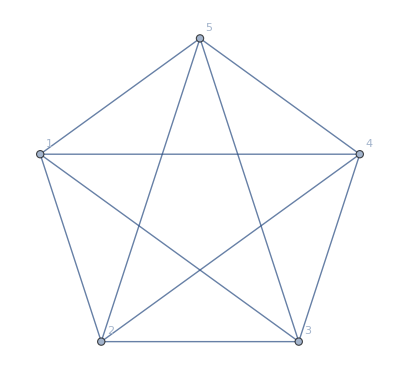

```mathematica
g=CompleteGraph[5,VertexLabels->"Name"]
```

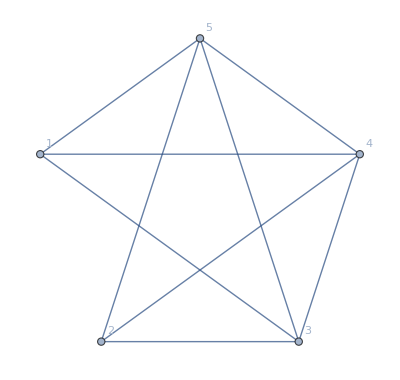
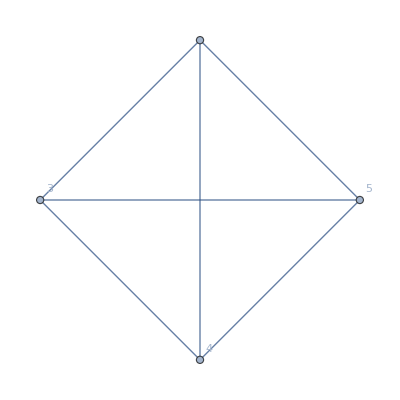

```mathematica
With[{e=UndirectedEdge[1,2]},{g2=EdgeDelete[g,e],EdgeContract[g,e]}]
```

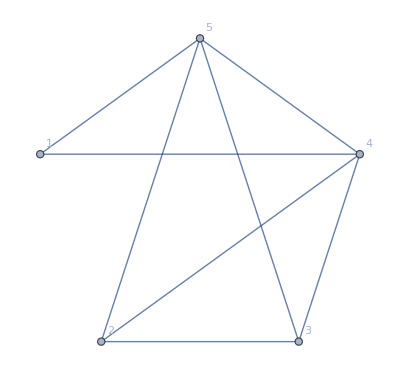
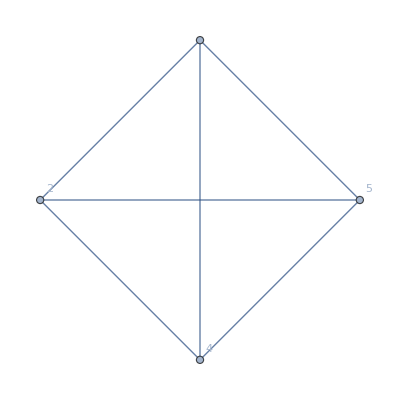

```mathematica
With[{e=UndirectedEdge[1,3]},{g3=EdgeDelete[g2,e],EdgeContract[g2,e]}]
```

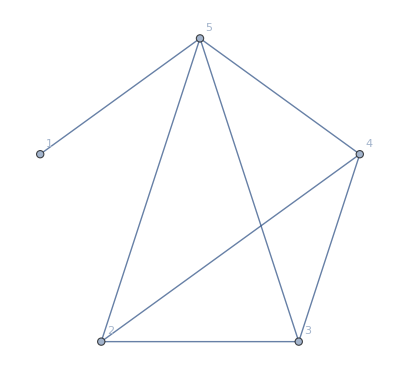
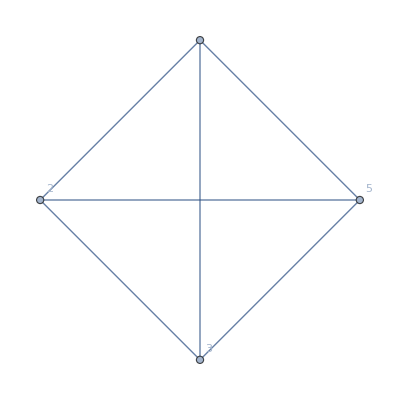

```mathematica
With[{e=UndirectedEdge[1,4]},{g4=EdgeDelete[g3,e],EdgeContract[g3,e]}]
```

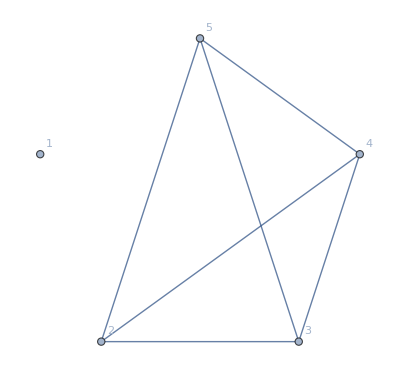
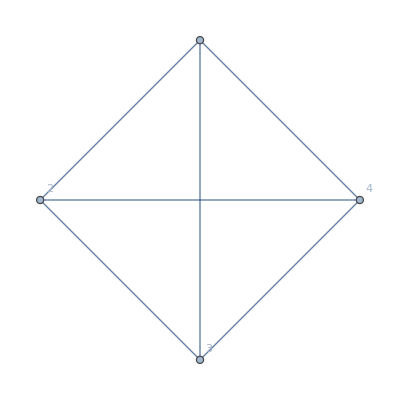

```mathematica
With[{e=UndirectedEdge[1,5]},{g5=EdgeDelete[g4,e],EdgeContract[g4,e]}]
```

## Sub k5

```mathematica
Table[Labeled[allGraphs5[z,"graph"],Style[z,ColourForKey[allGraphs5,z]] ],{z,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[VertexDelete[g,1],CompleteGraph[4]]
&&EdgeCount[g]==6
]
&]}]
```

{-Graphics-364}

```mathematica
allGraphs5[364,"colofour"]/.rep5
```

-Graphics-49207+-Graphics-36085+-Graphics-31711+-Graphics-30253+-Graphics-29524

```mathematica
allGraphs5[364,"colofourrealnull"]/.rep5Null
```

-6 -Graphics-728+2 -Graphics-666+2 -Graphics-546+-Graphics-488+2 -Graphics-218+-Graphics-72+2 -Graphics-26+-Graphics-168--Graphics-486--Graphics-162--Graphics-18--Graphics-54--Graphics-2--Graphics-6+-Graphics-0

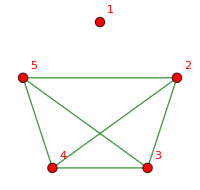
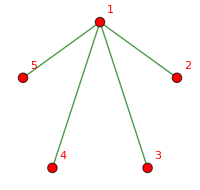
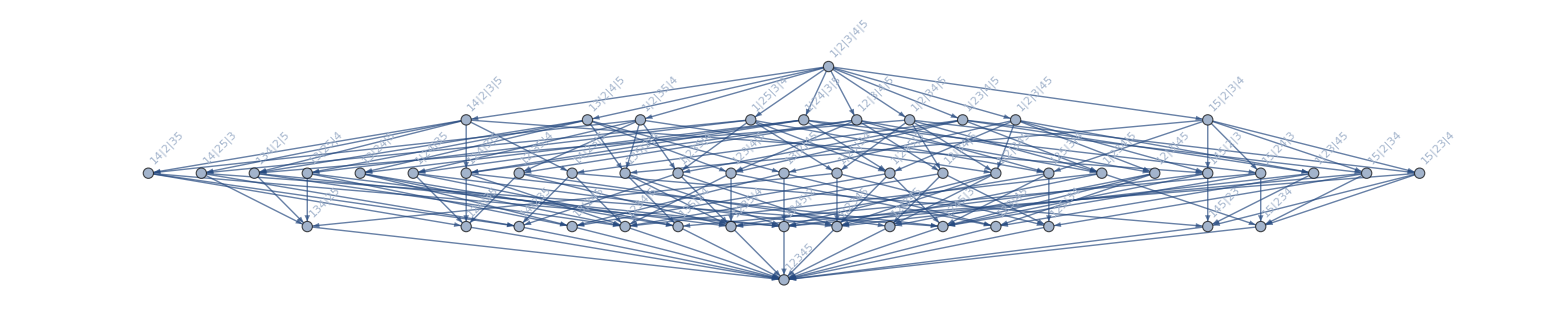
-Graphics-364 | -Graphics-29160
-Graphics-
-Graphics--6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5x^5-6 x^4+11 x^3-6 x^2
(x-3) (x-2) (x-1) x^2
 *  * 00096600
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood5[364]
```

```mathematica
Table[Labeled[allGraphs5[z,"graph"],Style[z,ColourForKey[allGraphs5,z]] ],{z,Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},
IsomorphicGraphQ[VertexDelete[VertexDelete[g,1],2],CompleteGraph[3]]
&&EdgeCount[g]==4
]
&]}]
```

VertexDelete::inv: The argument 2 in VertexDelete[Graph[<0>, <0>], 2] is not a valid vertex.

{-Graphics-19696,-Graphics-6574,-Graphics-2200,-Graphics-742,-Graphics-256,-Graphics-94,-Graphics-40}

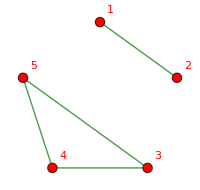
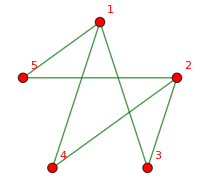
-Graphics-19696 | -Graphics-9828
-Graphics-
-Graphics--2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5x^5-4 x^4+5 x^3-2 x^2
(x-2) (x-1)^2 x^2
 *  * 00362881200
-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
SummaryPrintGood5[19696]
```